This notebook contains the proof that MutSel models will always correspond to a dN/dS≤1. The trick is to look at the forward and backward mutational path at the same time, i.e., we show that the total probability weight in going from i to j and going from j to i is always less than or equal to the sum of the frequencies of i and j.

Throughout this document, we write the frequency of amino acid i as x and the frequency of amino acid j as y. Further, we assume that x≤y. The fixation probability from x to y is:

```mathematica
p[x_,y_]:=(Log[y]-Log[x])/(1-x/y)
```

The sum of the probability weights going from x to y and from y to x is:

```mathematica
Simplify[x p[x,y]+y p[y,x]]
```

(2 x y (Log[x]-Log[y]))/(x-y)

We are going to show that this sum is less than or equal to x+y, i.e.,
	(2 x y (Log[x]-Log[y]))/(x-y) ≤ x+y,
for x, y≥0 and x≤y.

To this end, we define the function
	F(x,y) = x+y-(2 x y (Log[x]-Log[y]))/(x-y)
We thus want to show that F(x,y) ≥ 0 for x, y≥0 and x≤y. It is straightforward to show this for x=y:

```mathematica
F[x_,y_]:=x+y-(2 x y (Log[x]-Log[y]))/(x-y)
Limit[F[x,y], x->y]
```

0

We now show that the first derivative of F(x, y) is negative throughout x ∈ (0, y), thus proving that F(x, y) has to be monotonically decreasing in this interval and hence has to be ≥ 0 in this interval.

```mathematica
FullSimplify[D[F[x,y], x]]
```

((x-3 y) (x-y)+2 y^2 (Log[x]-Log[y]))/(x-y)^2

We can rewrite Log[x]-Log[y] as a series:

```mathematica
((x-3 y) (x-y)-2 y^2 Sum[(1-x/y)^n/n,{n,1,∞}])/(x-y)^2
```

((x-3 y) (x-y)+2 y^2 Log[x/y])/(x-y)^2

If we take only the first two terms of the series, we find that the expression becomes zero:

```mathematica
Simplify[((x-3 y) (x-y)-2 y^2 Sum[(1-x/y)^n/n,{n,1,2}])/(x-y)^2]
```

0

Thus, we can write the derivative of F(x, y) as: 
	(-2 y^2 Sum[(1-x/y)^n/n,{n,3,∞}])/(x-y)^2,
which is obviously negative.

Verification that the last statement was true:

```mathematica
FullSimplify[(-2 y^2 Sum[(1-x/y)^n/n,{n,3,∞}])/(x-y)^2]
```

((x-3 y) (x-y)+2 y^2 Log[x/y])/(x-y)^2

This concludes the proof.

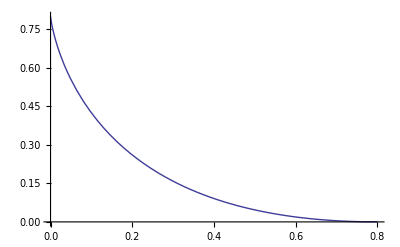

```mathematica
(*Plot showing that F[x, y] is positive.*)

Plot[x+y-(2 x y (Log[x]-Log[y]))/(x-y)/.y->.8, {x,0,.8}]
```

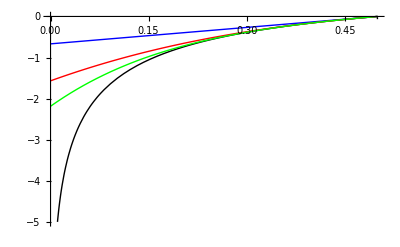

```mathematica
(*Plot showing that the derivative of F[x, y] is negative, and that the partial sums approximate it from above.*)

Plot[{((x-3 y) (x-y)+2 y^2 (Log[x]-Log[y]))/(x-y)^2/.y->.5,1/(x-y)^2(-2y^2(Sum[(1-x/y)^n/n,{n,3,3}]))/.y->.5,1/(x-y)^2(-2y^2(Sum[(1-x/y)^n/n,{n,3,5}]))/.y->.5,1/(x-y)^2(-2y^2(Sum[(1-x/y)^n/n,{n,3,7}]))/.y->.5},{x,0,0.5},PlotStyle->{Black,Blue, Red, Green}, PlotRange->{-5,0}]
```